### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/ExploringFundamentalsOfQuantumTheory

### Keywords

# Exploring Fundamentals of Quantum Theory

We will explore some important experiment in the foundation of quantum theory, using the Wolfram Quantum Framework. In this document, we will discuss quantum eraser, Elitzur-Vaidman bomb experiment, Hardy’s paradox, and quantum SWITCH.

## Quantum Eraser

If there is path information (stored somewhere, regardless of whether it is measured or not), there won’t be any interference. The mere presence of path information kills quantum interference. But by erasing the path information, one can recover quantum interference.  In the following setup, clicking all detectors corresponds to a no-interference case, and clicking of only D1 and D4 corresponds to the interference case.

### With path information: no interference

Prepare a series of quantum gates representing the above setup:

```mathematica
ops={"H","CX","H",{1},{2}};
```

Construct the quantum circuit:

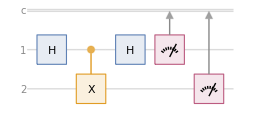

```mathematica
qc=QuantumCircuitOperator[ops];
qc["Diagram"]
```

Calculate the system evolution through each step:

```mathematica
steps=ComposeList[qc["Operators"],QuantumState[{"Register",2}]];
```

Show the states prior to measurement:

```mathematica
Grid[Transpose[{Style[#,Bold]&/@{"Initial state","After 1st Hadamard","After CNOT","After 2nd Hadamard"},#["Formula"]&/@steps[[;;-3]]}],Frame->All,Alignment->Left]
```

Initial state | 00
After 1st Hadamard | 00/(√2)+10/(√2)
After CNOT | 00/(√2)+11/(√2)
After 2nd Hadamard | 00/2+01/2+10/2-11/2

Get the probability of each outcome:

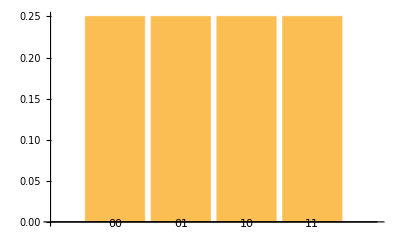

```mathematica
qc[QuantumState[{"Register",2}]]["ProbabilityPlot"]
```

### Erasing path information: interference

Prepare a series of quantum gates representing above setup:

```mathematica
ops={"H","CX","H","H"->2,{1},{2}};
```

Construct the quantum circuit:

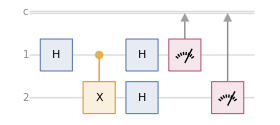

```mathematica
qc=QuantumCircuitOperator[ops];
qc["Diagram"]
```

Note that the Hadamard gate acting on 2nd qubit serves as quantum eraser.

Calculate the system evolution through each step:

```mathematica
steps=ComposeList[qc["Operators"],QuantumState[{"Register",2}]];
```

Show the states prior to measurement:

```mathematica
Grid[Transpose[{Style[#,Bold]&/@{"Initial state","After Hadamard on 1st qubit","After CNOT","After Hadamard on 1st qubit","After Hadamard on 2nd qubit"},#["Formula"]&/@steps[[;;-3]]}],Frame->All,Alignment->Left]
```

Initial state | 00
After Hadamard on 1st qubit | 00/(√2)+10/(√2)
After CNOT | 00/(√2)+11/(√2)
After Hadamard on 1st qubit | 00/2+01/2+10/2-11/2
After Hadamard on 2nd qubit | 00/(√2)+11/(√2)

Get the probability of each outcome:

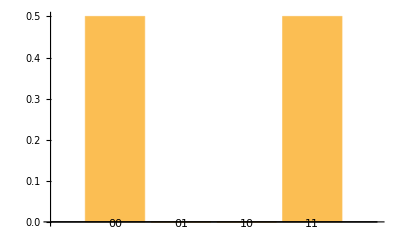

```mathematica
qc[QuantumState[{"Register",2}]]["ProbabilityPlot"]
```

## Elitzur-Vaidman bomb

Given quantum interference in a Mach-Zehnder setup with only one beam-splitter, a detector click can be inferred as the presence of an object along one arm of interferometer. However, due to the interference, there is a 50% chance that the photon does not move through that arm, as if one can infer the presence of that object without any interaction. To dramatize the case, think about that object as a bomb! This thought experiment is also called the interaction-free measurement.

### Simple case: 50:50 beam splitter

Prepare a series of quantum gates representing the above setup:

```mathematica
ops={"H","CX","H",{1},{2}};
```

Construct the quantum circuit:

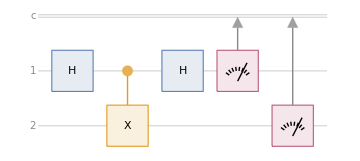

```mathematica
qc=QuantumCircuitOperator[ops];
qc["Diagram"]
```

Get the probability of each outcome:

```mathematica
prob=qc[]["Probabilities"]
```

<|00→1/4,01→1/4,10→1/4,11→1/4|>

Note that detecting 01 or 11 means that there is interaction with bomb (or a photon passed through the arm where the bomb is), while 00 means that, with the help of quantum interference, the bomb is detected with no interaction. Therefore, the efficiency rate  can be expressed as .

Calculate the probability:

```mathematica
prob[00]/(1-prob[10])
```

1/3

### Beyond 50:50 beam splitter

The Hadamard gate acts like a 50:50 beam splitter. One can replace it with a  gate, which is rotates along the -axis with an arbitrary angle θ:

```mathematica
QuantumOperator[{"RY",θ}]
```

QuantumOperator[…]

Compare the Hadamard gate with the   gate on the quantum state 0:

```mathematica
QuantumOperator["H"][QuantumState[{1,0}]]["Amplitudes"]
```

<|0→1/(√2),1→1/(√2)|>

```mathematica
FullSimplify/@QuantumOperator[{"RY",θ}][QuantumState[{1,0}]]["Amplitudes"]
```

<|0→Cos[θ/2],1→Sin[θ/2]|>

Note that the reflection will turn the qubit to 1, meaning it will be in the arm where the bomb is located.

Define a new quantum circuit using  :

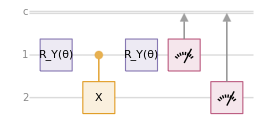

```mathematica
qc=QuantumCircuitOperator[{{"RY",θ},"CX",{"RY",θ},{1},{2}}];
qc["Diagram"]
```

Get the probability of each outcome:

```mathematica
prob=FullSimplify[#,θ∈Reals]&/@qc[QuantumState[{"Register",2}]]["Probabilities"]
```

<|00→Cos[θ/2]^4,01→Sin[θ/2]^4,10→Sin[θ]^2/4,11→Sin[θ]^2/4|>

Return the efficiency rate:

```mathematica
prob[00]/(1-prob[10])
```

Cos[θ/2]^4/(1-Sin[θ]^2/4)

Plot the efficiency rate:

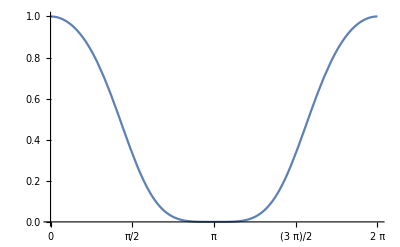

```mathematica
Plot[prob[00]/(1-prob[10]),{θ,0,2π},Ticks->{{0,π/2,π,(3 π)/2,2 π},Automatic},GridLines->{{0,π/2,π,(3 π)/2,2 π},Automatic}]
```

### Increasing efficiency by using a series of beam splitters

Define a new quantum circuit using  :

```mathematica
qcN[θ_,m_Integer]:=With[{n=m-1},QuantumCircuitOperator@Append[Table[{{"RY",θ},"CX"->{1,i+1}},{i,n}],{"RY",θ}]
];
```

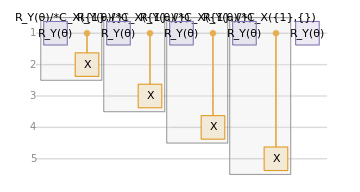

```mathematica
qcN[θ,5]["Diagram"]
```

Return the efficiency rate :

```mathematica
η[θ_,n_]:=Module[{ψr,ψt,ψf,pDet,pNul},
(*000,...,00*)
ψr=QuantumState[{"Register",n}];
(*100,...,00*)
ψt=QuantumOperator["X"]@QuantumState[{"Register",n}];
(*final state at the end of the cicruit*)
ψf=qcN[θ,n][ψr];
(*inner products wrt final state*)
{pDet,pNul}=Abs[First@#["Dagger"][ψf]["StateVector"]]^2&/@{ψr,ψt};
(*η*)
pDet/(1-pNul)
]
```

Plot the efficiency rate:

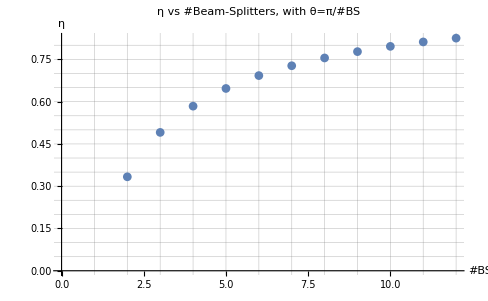

```mathematica
ListPlot[Table[{n,N@η[π/n,n]},{n,2,12}],GridLines->All,AxesLabel->{"#BS","η"},PlotLabel->"η vs #Beam-Splitters, with θ=π/#BS"]
```

Note that the dimension of matrices is , so increasing the number of qubits can lengthen the computation time.

## Hardy’s paradox

Define a new quantum circuit using :

```mathematica
qcH[θ1_,θ2_]:=QuantumCircuitOperator[{QuantumOperator[{"YRotation",θ1}],QuantumOperator[{"YRotation",θ2},{2}],QuantumOperator["Toffoli"],QuantumOperator[{"YRotation",π-θ1}],QuantumOperator[{"YRotation",π-θ2},{2}]}];
```

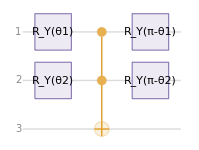

```mathematica
qcH[θ1,θ2]["Diagram"]
```

Get the final state:

```mathematica
final=qcH[θ1,θ2][QuantumState[{"Register",3}]];
```

Calculate the nonlocal probability for 000 (where one considers only cases where 3rd qubit is nonzero) as :

```mathematica
nonlocalProb=With[{prob=final["Amplitudes"]^2},prob[000]/(prob[000]+prob[100]+prob[010]+prob[110])]//FullSimplify[#,θ1∈Reals&&θ2∈Reals]&
```

(Sin[θ1]^2 Sin[θ2]^2)/(4 (3+Cos[θ1]+Cos[θ2]-Cos[θ1] Cos[θ2]))

Plot the nonlocal probability in 3D:

```mathematica
Plot3D[100.nonlocalProb,{θ1,0,2π},{θ2,0,2π},AxesLabel->{"θ1","θ2","% nonlocal probability"},Ticks->{{0,π/2,π,3π/2,2π},{0,π/2,π,3π/2,2π},Automatic}]
```

-Graphics3D-

Show the nonlocal probability as a density plot:

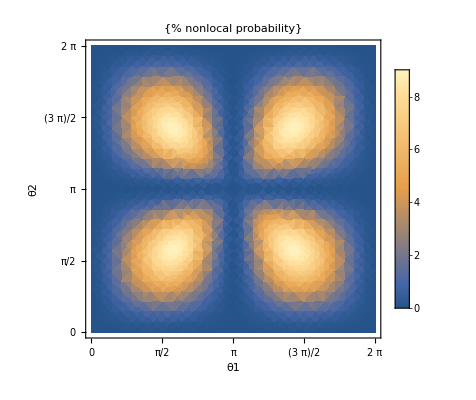

```mathematica
DensityPlot[100.nonlocalProb,{θ1,0,2π},{θ2,0,2π},AxesLabel->{"θ1","θ2","% nonlocal probability"},FrameTicks->{{0,π/2,π,3π/2,2π},{0,π/2,π,3π/2,2π}},PlotLegends->Automatic,PlotLabel->{"% nonlocal probability"}]
```

## Quantum Switch

The following example is based on a paper published in Nature Comm.

### Commuting example

Create a random 2D unitary operator:

```mathematica
u=QuantumOperator["RandomUnitary"];
```

Create two random commuting operators:

```mathematica
A=QuantumOperator[u@QuantumOperator[{"Phase",RandomReal[{0,2π}]}]@u["Dagger"],"Label"->"A"];
B=QuantumOperator[u@QuantumOperator[{"Phase",RandomReal[{0,2π}]}]@u["Dagger"],"Label"->"B"];
```

Consider the case where [A,B]=0:

```mathematica
(A@B-B@A)["Matrix"]//Chop//MatrixForm
```

(0 | 0
0 | 0)

The action of following circuit on an initial state + is 
0+1, which means if the qubit 1 is observed in the state 0 then it confirms that . If the qubit-1 is observed in the state 1 then it confirms that .

Construct the circuit based on a quantum switch (defined in the initialization):

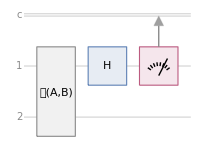

```mathematica
qc=QuantumCircuitOperator[{QuantumOperator[{"Switch",A,B}],QuantumOperator["H"],QuantumMeasurementOperator[]}];
qc["Diagram"]
```

Get the tensor product for +RandomPure:

```mathematica
ψ0=QuantumTensorProduct[QuantumState["Plus"],QuantumState["RandomPure"]]
```

QuantumState[…]

Perform the measurement:

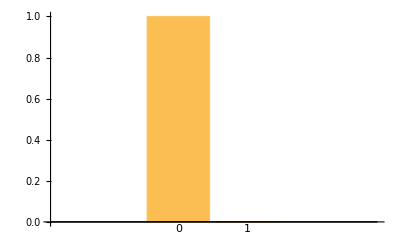

```mathematica
qc[ψ0]["ProbabilityPlot"]
```

The result confirms the commuting case.

### Anti-commuting example

Create a random 2D unitary operator:

```mathematica
u=QuantumOperator["RandomUnitary"];
```

Create two commuting operators:

```mathematica
A=QuantumOperator[u@QuantumOperator["X"]@u["Dagger"],"Label"->"A"];
B=QuantumOperator[u@QuantumOperator["Z"]@u["Dagger"],"Label"->"B"];
```

Note that we consider the case where {A,B}=0:

```mathematica
(A@B+B@A)["Matrix"]//Chop//MatrixForm
```

(0 | 0
0 | 0)

The action of following circuit on an initial state +  is as follows: 0+1, which means if qubit 1 is observed in the state 0 then it confirms ; and if qubit 1 is observed in the state 1 then it confirms .

Construct the circuit based on a quantum switch (defined in the initialization):

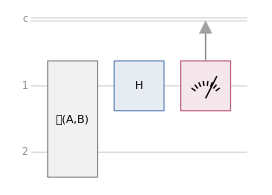

```mathematica
qc=QuantumCircuitOperator[{QuantumOperator[{"Switch",A,B}],QuantumOperator["H"],QuantumMeasurementOperator[]}];
qc["Diagram"]
```

Get the tensor product for  +RandomPure:

```mathematica
ψ0=QuantumTensorProduct[QuantumState["Plus"],QuantumState["RandomPure"]]
```

QuantumState[…]

Perform the measurement:

```mathematica
qc[ψ0]["ProbabilityPlot"]
```

-Graphics-

The result confirms the anti-commuting case.

More About

Related Tech Notes

Related Wolfram Education Group Courses